## What’s Here

This notes shows some primary calculations on the propulsion system using only gas.

## Pre

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\USERS\Guokr\Documents\GitHub\WhyMathematica\Physics\AttackOnTitan

Image size is defined

```mathematica
imgSize=500;
```

## Fundamental Physics & Mathematics

This is something like the Tsiolkovsky rocket equation.

m(d v)/(d t)=-v_e (d m)/(d t)

Next we assume that the velocity of gas in rocket frame v_e is constant.

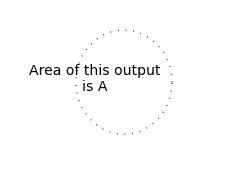

We assume the outlet of the gas is a constant area, and the density of gas at the outlet is ρ (assuming this is constant since we already assumed that the output velocity is constant). Thus we can calculate the mass leakage of the system which works as the propulsion of the equipment.

v-v_0=v_e Log[(μ ρ v_e A t_0-m_0)/(μ ρ v_e A t-m_0)]

It is good to make v_0=0, t_0=0.

v=v_e Log[m_0/(-μ ρ v_e A t+m_0)]

Acceleration

D[v_e Log[m_0/(-μ ρ v_e A t+m_0)],t]

(A ρ v_e^2)/(m_0-μ A t ρ v_e)

#### More Real

Orifice leakage model.

Now we have to determine the velocity of the gas output. A function gives us the result, that is leakage current of gas is

Q=μ A  ρ_e √((2Δ P)/ρ)

Here we can choose μ∈[0.60,0.62].
For simplicity, ρ_e≈ρ

Q is just the product of A and v_e and ρ_e, Q=v_e A, i.e.,

v_e=√((2 Δ P)/ρ)

Substitution,

v=√((2(P-P_0))/(P/P_0 ρ_0))Log[m_0/(m_0-P/P_0 ρ_0 A μ √((2(P-P_0))/(P/P_0 ρ_0))t)]

ve Log[m0/(m0-ρ ve A t)]/.{ve→√2  √((P-P0)/(P/P0 ρ0)) ,ρ→(P ρ0)/P0}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Before we use this expression, we need to split the m0 into two parts, one is the mass of gas, the other part is the mass of the body, volume, everything else.

m0 -> M0+m0

result is

√2 μ √(((P-P0) P0)/(P ρ0)) Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]/.{m0→(M0+m0)}

√2 μ √(((P-P0) P0)/(P ρ0)) Log[(m0+M0)/(m0+M0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)]

Acceleration

D[√2 μ Log[m0/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),t]

(2 A (P-P0) μ^2)/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)

### Air Drag

(*Parasitic air drag can be decomposed into three parts,*)

Just the simplest case,

-f(v)=m dv/dt-v_e^2 ρ A μ

dm=-μ v_e ρ A dt

m=m_0-μ ρ v_e A t

Case 1

f=-k1 v

In this case

v=1/k1( ρ v_e^2 A - (m_0 - ρ μ v_e A t)^(k1/(ρ v_e A)) )

Case 2

-f=1/2 ρ0 v^2 C_D A0

We can calculate the velocity of fly object:

dv/dt=(v_e^2 Q ρ - μ ρ_0 S v^2)/(m0 - (∫_0)^t ρ v_e Q dt)

Finally we have the differential equation

dv/(-1/2 ρ_0 C_D A_0 v^2+v_e^2 ρ A μ)=dt/(m_0- μ ρ v_e A t)

dv/(μ A ρ v_e^2-1/2 v^2 A_0 C_D ρ_0)==dt/(m_0-μ A t ρ v_e)

```mathematica
Integrate[1/(μ A ρ ve^2-1/2 v^2 A0 C0 ρ0),v]
Integrate[1/(m0-μ A t ρ ve),t]
```

(√2 ArcTanh[(√A0 √C0 v √ρ0)/(√2 √A ve √μ √ρ)])/(√A √A0 √C0 ve √μ √ρ √ρ0)

-Log[m0-A t ve μ ρ]/(A ve μ ρ)

```mathematica
Assumptions[{v∈Reals,m0-A t ve μ ρ>0,(√A0|| √C0|| √ρ0||√A|| √μ|| √ρ)∈Reals}]
```

Assumptions[{v∈Reals,m0-A t ve μ ρ>0,(√A0||√C0||√ρ0||√A||√μ||√ρ)∈Reals}]

```mathematica
Solve[(√2 ArcTanh[(√A0 √C0 v √ρ0)/(√2 √A ve √μ √ρ)])/(√A √A0 √C0 ve √μ √ρ √ρ0)==Log[m0]/(A ve μ ρ)-Log[m0-A t ve μ ρ]/(A ve μ ρ),v]
airVSol=v/.%[[1]][[1]]/.{ve->√2 √((P-P0)/(P/P0 ρ0)) ,ρ->(P ρ0)/P0}
D[%,t]
```

{{v→(√2 √A ve √μ √ρ Tanh[(√2 √A0 √C0 √ρ0 Log[m0]-√2 √A0 √C0 √ρ0 Log[m0-A t ve μ ρ])/(2 √A √μ √ρ)])/(√A0 √C0 √ρ0)}}

(2 √A √μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√2 √A0 √C0 √ρ0 Log[m0]-√2 √A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(2 √A √μ √((P ρ0)/P0))])/(√A0 √C0 √ρ0)

(2 A (P-P0) μ Sech[(√2 √A0 √C0 √ρ0 Log[m0]-√2 √A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(2 √A √μ √((P ρ0)/P0))]^2)/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)

### Air Drag and Pressure drop

## Analysis

### Part 1 Simple Case

#### Simple Examination

Now we just show the scheme of this result

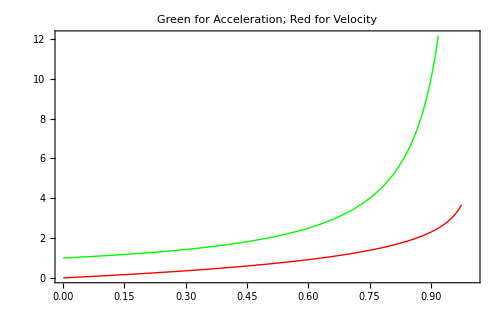

```mathematica
Show[Table[Plot[func[[1]],{t,0,1},PlotStyle->func[[2]],AxesOrigin->{0,0},Frame->True,ImageSize->imgSize],{func,{{1/(1-t),Green},{Log[1/(1-t)],Red}}}],PlotLabel->"Green for Acceleration; Red for Velocity"]
```

#### More Physics

Maybe we want to know the physics of different parameters.

```mathematica
Manipulate[Grid[{{Plot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]},{LogPlot[ve Log[m0/(m0-ρ ve A t)],{t,0,m0/ρ ve A},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]}}],{{ve,1,"Velocity of Gas"},1,10,1},{{m0,1,"Initial Mass of Equipment"},1,10,1},{{ρ,1,"Density of Gas at Outlet"},1,50,1},{{A,1,"Area of Outlet"},1,10,1}]
```

#### Even more real

If we put every number in it,

```mathematica
Manipulate[
   "Leakage Constant:"<>ToString[μ]<>";\n"
"Constant Pressure:"<>ToString[P]<>";\n"
"Initial Mass of Gas:"<>ToString[m0]<>";\n"
"Density of Air:"<>ToString[ρ0]<>";\n"
"Area of Outlet:"<>ToString[A]<>";\n"
"Mass of Everything Else:"<>ToString[M0]<>";\n"
Grid[{{Block[{P0=101325},Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]]}}],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Gas"},1,50,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.001,"Area of Outlet"},0.001,1,0.001},{{M0,50,"Mass of Everything Else"},10,100,1}]
```

### Importance of Weight of user

Check the effect of one’s weight, that is M0.

```mathematica
weightList1=Table[Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,A=0.001},
Grid[{{
"Mass of Everything Else:"<>ToString[M0]<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";\n"
},{
Grid[{{Block[{P0=101325},
Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize,PlotRange->{{0,25},{0,400}}]]},{Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize,PlotRange->{{0,25},{0,70}}]]}}]}}]],{M0,20,80,10}];
```

```mathematica
ListAnimate[weightList1];
```

```mathematica
weightExp1=Export["Export/weightList1.gif",weightList1,"DisplayDurations"->1.5]
```

Export/weightList1.gif

Calculate the effect of  M0 at 5th second.

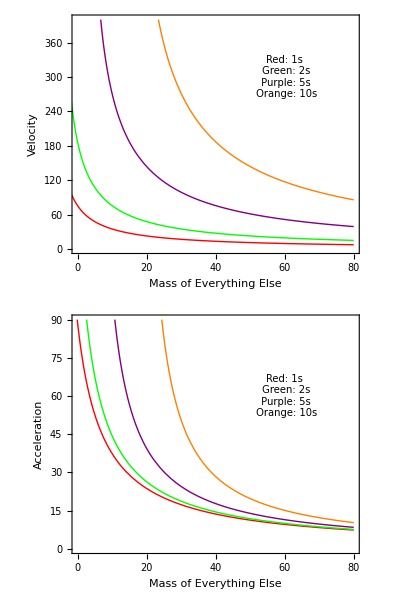
Results at different time t;
Leakage Constant:0.6;Constant Pressure:1000000;Initial Mass of Gas:10;
Density of Air:1.16;Area of Outlet:0.001;

-Graphics-

```mathematica
Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,A=0.001},
Grid[{{
"Results at different time t"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";\n"
},{
Grid[{{
Block[{P0=101325},
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{M0,-m0+(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0,80},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Mass of Everything Else","Velocity"},ImageSize->imgSize,PlotRange->{{0,80},{0,400}}],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,300}]]
]
},{Block[{P0=101325},
Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{M0,-m0+(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0,80},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Mass of Everything Else","Acceleration"},ImageSize->imgSize,PlotRange->{{0,80},{0,90}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,60}]]
]}}]}}]]
```

Pressure analysis

Check pressure of the gas.

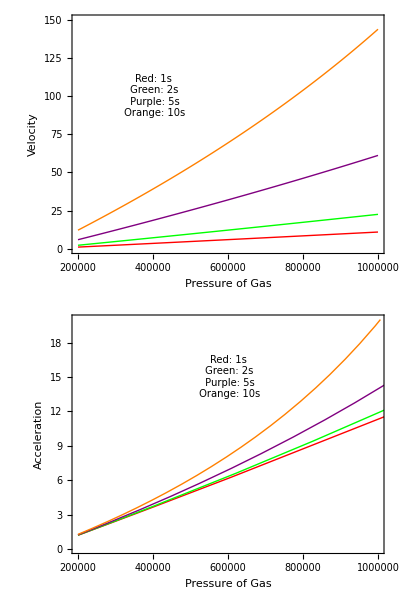
Results at different pressure P;
Leakage Constant:0.6;Constant Pressure:Initial Mass of Gas:10;
Density of Air:1.16;Area of Outlet:0.001;Mass of everything else:50;

-Graphics-

```mathematica
Block[{μ=0.6,M0=50,m0=10,ρ0=1.16,A=0.001,P0=101325},
Grid[{{
"Results at different pressure P"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Area of Outlet:"<>ToString[A]<>";"<>"Mass of everything else:"<>ToString[M0]<>";\n"
},{
Grid[{{
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{P,200000,1000000},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Pressure of Gas","Velocity"},ImageSize->imgSize,PlotRange->{Automatic,{0,150}}],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{4*10^5,100}]]
},{Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{P,200000,P/.Solve[M0+m0==(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0][[1]]},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Pressure of Gas","Acceleration"},ImageSize->imgSize,PlotRange->{{200000,1000000},{0,20}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{6*10^5,15}]]
}}]}}]]
```

Size of the outlet

The results for different area of outlet.

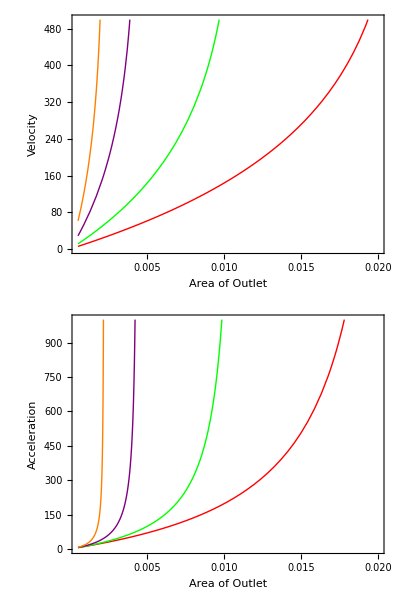
Results at different area of outlet;
Leakage Constant:0.6;Constant Pressure:1000000;Initial Mass of Gas:10;
Density of Air:1.16;Mass of Everything Else:50;

-Graphics-

```mathematica
Block[{μ=0.6,P=1000000,m0=10,ρ0=1.16,M0=50,P0=101325},
Grid[{{
"Results at different area of outlet"<>";"},
{"Leakage Constant:"<>ToString[μ]<>";"<>"Constant Pressure:"<>ToString[P]<>";"<>"Initial Mass of Gas:"<>ToString[m0]<>";\n"<>"Density of Air:"<>ToString[ρ0]<>";"<>"Mass of Everything Else:"<>ToString[M0]<>";\n"
},{
Grid[{{
Show[Table[Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{A,0.0005,0.02},Frame->True,PlotStyle->t[[2]],PlotRange->{{0.0005,0.02},{0,500}},FrameLabel->{"Area of Outlet","Velocity"},ImageSize->imgSize],{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,300}]]
},{
Show[Table[Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{A,0.0005,(M0+m0)/(√2 P t[[1]] μ √(((P-P0) P0)/(P ρ0)) ρ0)P0},Frame->True,PlotStyle->t[[2]],FrameLabel->{"Area of Outlet","Acceleration"},ImageSize->imgSize,PlotRange->{{0.0005,0.02},{0,1000}}]
,{t,{{1,Red},{2,Green},{5,Purple},{10,Orange}}}]
,Epilog->Inset[Style["Red: 1s\n Green: 2s\n Purple: 5s\n Orange: 10s",10],{60,60}]]
}}]}}]]
```

### Air Drag

However, the air drag could be quite significant in this case since the velocity is so large.

Before we do the detailed calculation, let’s have a look at the air drag and the propulsion force by airjet.

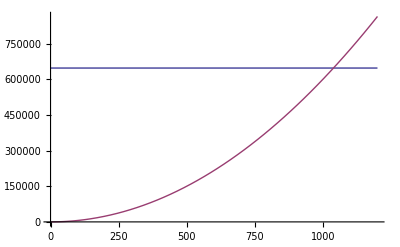

```mathematica
Block[
{P0=101325,M0=50,ρ0=1.2,μ=0.6,m0=10,A=1,A0=1,C0=1,P=1000000},Plot[{A P/P0 ρ0 (√2 μ √((P-P0)/(P/P0 ρ0)))^2,1/2 v^2 A0 C0 ρ0},{v,0,1200}]
]
```

#### Case 1 friction proportional to velocity.

f = k1 v. I don’t know

#### Case 2

v is (2 √A √μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[(√2 √A0 √C0 √ρ0 Log[m0+M0]-√2 √A0 √C0 √ρ0 Log[M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])/(2 √A √μ √((P ρ0)/P0))])/(√A0 √C0 √ρ0)

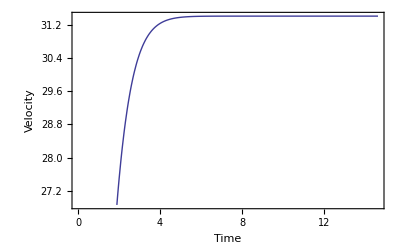

```mathematica
Block[
{P0=101325,M0=50,ρ0=1.2,μ=0.6,m0=10,A=0.01,A0=1,C0=2,P=200000},
{airDragCase2Plt=Plot[1/(√A0 √C0 √ρ0)2 √A √μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[1/(2 √A √μ √((P ρ0)/P0))(√2 √A0 √C0 √ρ0 Log[m0+M0]-√2 √A0 √C0 √ρ0 Log[m0+M0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])],{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8]
}
];
airDragCase2Plt
```

```mathematica
Manipulate[
   "Leakage Constant:"<>ToString[μ]<>";\n"
"Constant Pressure:"<>ToString[P]<>";\n"
"Initial Mass of Gas:"<>ToString[m0]<>";\n"
"Density of Air:"<>ToString[ρ0]<>";\n"
"Area of Outlet:"<>ToString[A]<>";\n"
"Mass of Everything Else:"<>ToString[M0]<>";\n"
Grid[{{Grid[{{Block[{P0=101325},Plot[1/(√A0 √C0 √ρ0)2 √A √μ √(((P-P0) P0)/(P ρ0)) √((P ρ0)/P0) Tanh[1/(2 √A √μ √((P ρ0)/P0))(√2 √A0 √C0 √ρ0 Log[m0+M0]-√2 √A0 √C0 √ρ0 Log[m0+M0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])],{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8,PlotLabel->"With Air Drag"]]
,
Block[{P0=101325},Plot[√2 μ Log[(m0+M0)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)] √(((P-P0) P0)/(P ρ0)),{t,0,(m0+M0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Velocity"},ImageSize->imgSize*0.8,PlotLabel->"Without Air Drag"]]}}]},
{Grid[{{
Block[{P0=101325},Plot[(2 A (P-P0) μ Sech[1/(2 √A √μ √((P ρ0)/P0))(√2 √A0 √C0 √ρ0 Log[m0]-√2 √A0 √C0 √ρ0 Log[m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0])]^2)/(m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8,PlotLabel->"With Air Drag"]]
,Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8,PlotLabel->"Without Air Drag"]]
}}]}}],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Gas"},1,50,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.001,"Area of Outlet"},0.001,1,0.001},{{M0,50,"Mass of Everything Else"},10,100,1},
{{A0,1,"Area of Body"},0.5,2},
{{C0,1.6,"Drag Coeficient"},0.4,2},ControlPlacement->Bottom]
```

### Consider the pressure drop in the air tank

#### Some preliminary materials

Density of air at 30 C is 1.16kg/m^3 . For simplicity  we use 30 C as the general temperature of the system. That is, pressure at temperature T with a volume V for mass m

P_i/m_i=1/M(R T)/V=1/(2.9*10^-2 kg/mol)(8.31*300)/(2*0.2*0.2)=1.07457×10^6Pa/kg

Then we can calculate the mass change with time. Here m is the mass of gas!!!

dm = μ A √(2 ρ0/P0 m/m0 pi (pi/m0 m-P0))dt

```mathematica
airDragPDropMassLHS=Integrate[1/(√(m(pi/m0 m-P0))),m]//FullSimplify
%/.{m->m0}
airDragPDropMassRHS=μ A √(2 ρ0/P0 pi/m0)t
```

(2 √m √m0 √(-P0+(m pi)/m0) Log[√m pi+√m0 √pi √(-P0+(m pi)/m0)])/(√pi √(m (-P0+(m pi)/m0)))

(2 m0 √(-P0+pi) Log[√m0 pi+√m0 √pi √(-P0+pi)])/(√pi √(m0 (-P0+pi)))

√2 A t μ √((pi ρ0)/(m0 P0))

So the final equation for the mass evolution is

```mathematica
Solve[(2 √m √m0 √(-P0+(m pi)/m0) Log[√m pi+√m0 √pi √(-P0+(m pi)/m0)])/(√pi √(m (-P0+(m pi)/m0)))-(2 m0 √(-P0+pi) Log[√m0 pi+√m0 √pi √(-P0+pi)])/(√pi √(m0 (-P0+pi)))==-√2 A t μ √((pi ρ0)/(m0 P0)),m];
airDragPDropMassSol=%[[1]]
airDragPDropMassFunc[pi_,m0_,A_,μ_,ρ0_,P0_]=m/.airDragPDropMassSol
airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0]
```

{m→(ⅇ^(-(√2 A pi t μ √ρ0)/(m0 √P0)) (-m0 P0+2 ⅇ^((√2 A pi t μ √ρ0)/(m0 √P0)) m0 P0-ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 P0+2 m0 pi+2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 pi+2 m0 √pi √(-P0+pi)-2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 √pi √(-P0+pi)))/(4 pi)}

(ⅇ^(-(√2 A pi t μ √ρ0)/(m0 √P0)) (-m0 P0+2 ⅇ^((√2 A pi t μ √ρ0)/(m0 √P0)) m0 P0-ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 P0+2 m0 pi+2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 pi+2 m0 √pi √(-P0+pi)-2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 √pi √(-P0+pi)))/(4 pi)

(ⅇ^(-(√2 A pi t μ √ρ0)/(m0 √P0)) (-m0 P0+2 ⅇ^((√2 A pi t μ √ρ0)/(m0 √P0)) m0 P0-ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 P0+2 m0 pi+2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 pi+2 m0 √pi √(-P0+pi)-2 ⅇ^((2 √2 A pi t μ √ρ0)/(m0 √P0)) m0 √pi √(-P0+pi)))/(4 pi)

Plot out the evolution of mass

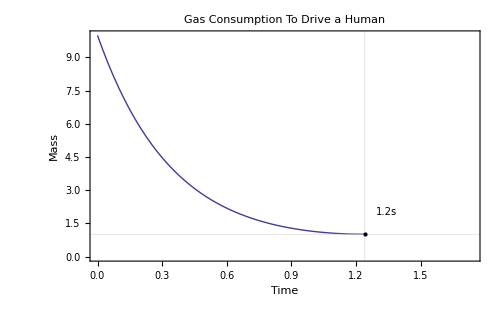

```mathematica
Block[
{P0=101325,ρ0=1.2,μ=0.6,m0=10,A=0.01,A0=1,C0=2,pi=1000000},
{Plot[m/.airDragPDropMassSol,{t,0,tempt1=t/.FindRoot[MinValue[m/.airDragPDropMassSol,t]==m/.airDragPDropMassSol,{t,1}]},PlotRange->{{0,tempt1+0.5},{0,10}},Frame->True,FrameLabel->{"Time","Mass"},GridLines->{{tempt1=t/.FindRoot[MinValue[m/.airDragPDropMassSol,t]==m/.airDragPDropMassSol,{t,1}]},{tempMin1=MinValue[m/.airDragPDropMassSol,t]}},Epilog-> {PointSize[Medium],Point[{tempt1,tempMin1}]},Prolog->Inset[Style[ToString[NumberForm[tempt1,2]]<>"s",10],{tempt1+0.1,tempMin1+1},{Center,Center}],ImageSize->imgSize,PlotLabel->"Gas Consumption To Drive a Human"]
}
]
```

It’s true that the mass of the gas can be determined by the pressure and the volume of the gas tank.

m0 = pi/(1/M(R T)/V)

We would like to use a standard volume of V = 0.08 m^3. For air, M=2.9*10^-2 kg/mol.

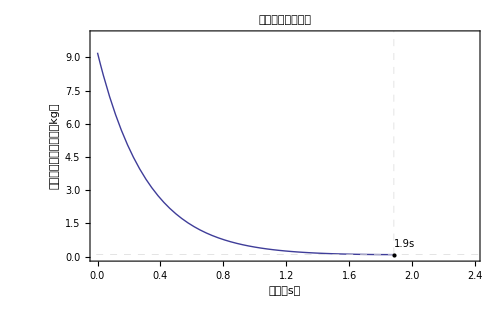

```mathematica
conGasCons=Block[
{P0=101325,ρ0=1.2,μ=0.6,A=0.001,A0=1,C0=2,pi=10000000,M=2.9*10^-2,R=8.31,T=303,V=0.08},
m0= pi/(1/M(R T)/V);

Plot[m/.airDragPDropMassSol,{t,0,tempt1=t/.FindRoot[MinValue[m/.airDragPDropMassSol,t]==m/.airDragPDropMassSol,{t,1}]},PlotRange->{{0,tempt1+0.5},{0,10}},Frame->True,FrameLabel->{"时间（s）","气瓶中剩余气体质量（kg）"},GridLines->{{{tempt1,Dashed}},{{tempMin1=MinValue[m/.airDragPDropMassSol,t],Dashed}}},Epilog-> {PointSize[Medium],Point[{tempt1,tempMin1}]},Prolog->Inset[Style[ToString[NumberForm[tempt1,2]]<>"s",10],{tempt1+0.07,tempMin1+0.5},{Center,Center}],ImageSize->imgSize,PlotLabel->"气瓶中气体的质量"]
]
```

This is amusing!!!! With such a pressure, the bottle stores only so little gas.

The leakage velocity ve

v_e=√(2(P-P0)/ρ)=√(2 P0/ρ0(1-P0 mi/pi 1/m))

```mathematica
√(2 P0/ρ0(1-P0 mi/pi 1/m))/.{mi->M0+m0}
```

√2 √((P0 (1-((m0+M0) P0)/(m pi)))/ρ0)

AND we still have an important equation to solve:

-ρ0 v^2 A0 C0 1/2=m dv/dt-ve dm/dt

```mathematica
-1/2 A0 C0 v^2 ρ0==(dv m)/dt-(dm ve)/dt/.{ve->√2 √((P0 (1-(m0 P0)/(m pi)))/ρ0),dm->μ A √(2 ρ0/P0 m pi/m0(m pi/m0-P0))dt}
airDragPDropVEqn=(-1/2 A0 C0 v[t]^2 ρ0+0.658882282406323 A μ √((P0 (1-(9.213917781669863 P0)/(m pi)))/ρ0) √((m pi (-P0+0.10853146551724138 m pi) ρ0)/P0))/(m+M0)==v'[t]/.airDragPDropMassSol
airDragPDropVEqnFunc[m0_]=(-1/2 A0 C0 v[t]^2 ρ0+0.658882282406323 A μ √((P0 (1-(9.213917781669863 P0)/(m pi)))/ρ0) √((m pi (-P0+0.10853146551724138 m pi) ρ0)/P0))/(m+M0)==v'[t]/.airDragPDropMassSol
```

-1/2 A0 C0 v^2 ρ0==(dv m)/dt-0.760812 A μ √((P0 (1-(6.91044 P0)/(m pi)))/ρ0) √((m pi (-P0+0.144709 m pi) ρ0)/P0)

(0.329441 A μ √((P0 (1-(36.8557 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0)/(-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi))))/ρ0) √(1/P0ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi)) (-P0+0.0271329 ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi))) ρ0)-1/2 A0 C0 ρ0 v[t]^2)/(M0+1/(4 pi)ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi)))==v'[t]

(0.329441 A μ √((P0 (1-(36.8557 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0)/(-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi))))/ρ0) √(1/P0ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi)) (-P0+0.0271329 ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi))) ρ0)-1/2 A0 C0 ρ0 v[t]^2)/(M0+1/(4 pi)ⅇ^(-(0.204649 A pi t μ √ρ0)/(√P0)) (-6.91044 P0+13.8209 ⅇ^((0.204649 A pi t μ √ρ0)/(√P0)) P0-6.91044 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) P0+13.8209 pi+13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) pi+13.8209 √pi √(-P0+pi)-13.8209 ⅇ^((0.409298 A pi t μ √ρ0)/(√P0)) √pi √(-P0+pi)))==v'[t]

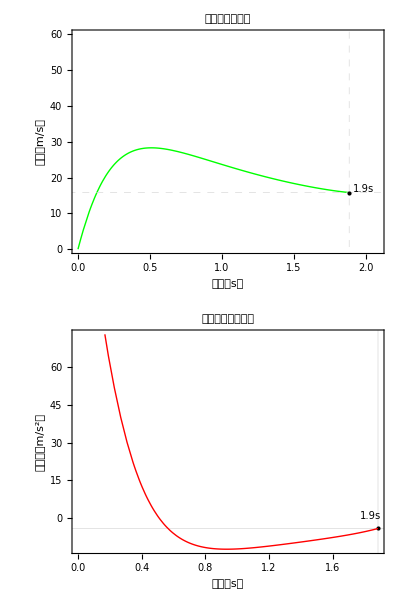

```mathematica
Block[
{P0=101325,M0=50,ρ0=1.2,μ=0.6,A=0.001,A0=1,C0=2,pi=10000000,M=2.9*10^-2,R=8.31,T=303,V=0.08},
Grid[{{m0= pi/(1/M(R T)/V);
airDragPDropVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,tempt2=t/.FindRoot[MinValue[m/.airDragPDropMassSol,t]==m/.airDragPDropMassSol,{t,1}]}];
Plot[v[t]/.airDragPDropVSol
,{t,0,tempt2=t/.FindRoot[MinValue[m/.airDragPDropMassSol,t]==m/.airDragPDropMassSol,{t,1}]},PlotRange->{{0,tempt1+0.2},{0,60}},PlotStyle->Green,Frame->True,FrameLabel->{"时间（s）","速度（m/s）"},GridLines->{{{tempt2,Dashed}},{{velocitytemp2=v[t]/.airDragPDropVSol[[1]]/.{t->tempt2},Dashed}}},Epilog-> {PointSize[Medium],Point[{tempt2,velocitytemp2}]},Prolog->Inset[Style[ToString[NumberForm[tempt2,2]]<>"s",10],{tempt2+0.1,velocitytemp2+1},{Center,Center}],ImageSize->imgSize,PlotLabel->"速度随时间变化",ImagePadding->{{40,10},{40,10}}]},
{
Plot[Evaluate[accelerationtemp2=D[v[t]/.airDragPDropVSol[[1]],t]],{t,0,tempt2},PlotStyle->Red,Frame->True,FrameLabel->{"时间（s）","加速度（m/s^2）"},GridLines->{{tempt2},{accelerationtemp2/.{t->tempt2}}},Epilog-> {PointSize[Medium],Point[{tempt1,accelerationtemp2/.{t->tempt2}}]},Prolog->Inset[Style[ToString[NumberForm[tempt1,2]]<>"s",10],{tempt1-0.05,5+accelerationtemp2/.{t->tempt2}},{Center,Center}],ImageSize->imgSize,PlotLabel->"加速度随时间变化",ImagePadding->{{40,10},{40,10}}]
}}]
]
```

#### 一些因素的分析

使用者的体重以及其他的所有的装备的重量（包括气瓶）的影响，M0 的影响

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

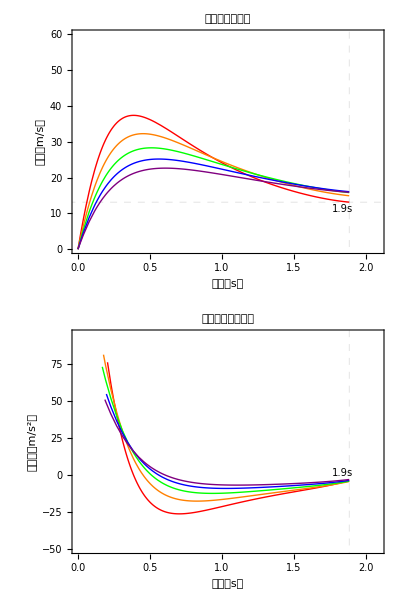

```mathematica
conM0Var=Block[{P0=101325,ρ0=1.2,μ=0.6,A=0.001,A0=1,C0=2,pi=10000000,M=2.9*10^-2,R=8.31,T=303,V=0.08},
Grid[{{m0= pi/(1/M(R T)/V);pltStyle={Red,Orange,Green,Blue,Purple};
Show[Table[conM0VarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conM0Vartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
Plot[v[t]/.conM0VarVSol
,{t,0,conM0Vartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]},PlotRange->{{0,conM0Vartempt2+0.2},{0,60}},PlotStyle->pltStyle[[Position[{30,40,50,60,70},M0][[1]][[1]]      ]],Frame->True,FrameLabel->{"时间（s）","速度（m/s）"},GridLines->{{{conM0Vartempt2,Dashed}},{{conM0Varvelocitytemp2=v[t]/.conM0VarVSol[[1]]/.{t->conM0Vartempt2},Dashed}}},Prolog->Inset[Style[ToString[NumberForm[conM0Vartempt2,2]]<>"s",10],{conM0Vartempt2-0.05,conM0Varvelocitytemp2-2},{Center,Center}],ImageSize->imgSize,PlotLabel->"速度随时间变化",ImagePadding->{{40,10},{40,10}}]
,{M0,{30,40,50,60,70}}]
]
},{
Show[
conM0VarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conM0Vartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
Table[Plot[Evaluate[conM0Varaccelerationtemp2=D[v[t]/.conM0VarVSol[[1]],t]],{t,0,conM0Vartempt2},PlotStyle->pltStyle[[Position[{30,40,50,60,70},M0][[1]][[1]]      ]],Frame->True,FrameLabel->{"时间（s）","加速度（m/s^2）"},
GridLines->{{{conM0Vartempt2,Dashed}},{}},Prolog->Inset[Style[ToString[NumberForm[conM0Vartempt2,2]]<>"s",10],{conM0Vartempt2-0.05,5+conM0Varaccelerationtemp2/.{t->conM0Vartempt2}},{Center,Center}],ImageSize->imgSize,PlotLabel->"加速度随时间变化",ImagePadding->{{40,10},{40,10}}],{M0,{30,40,50,60,70}}]
,PlotRange->{{0,conM0Vartempt2+0.2},{-50,95}}]
}}]
]
```

喷气孔的面积

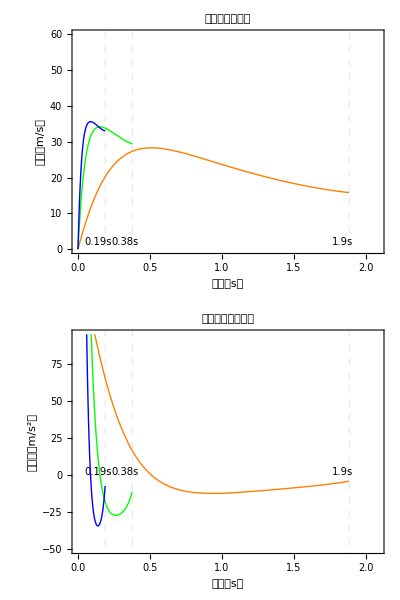

```mathematica
conAVar=Block[{P0=101325,ρ0=1.2,μ=0.6,M0=50,A0=1,C0=2,pi=10000000,M=2.9*10^-2,R=8.31,T=303,V=0.08},
Grid[{{m0= pi/(1/M(R T)/V);pltStyle={Red,Orange,Green,Blue,Purple};
conAVarAcceGridLinesX=Table[{t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}],Dashed},{A,{0.001,0.005,0.01}}];
conAVarGridLinesX={};
Show[
Table[
conAVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conAVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
conAVarGridLinesX=Append[conAVarGridLinesX,{conAVartempt2,Dashed}];
Plot[v[t]/.conAVarVSol
,{t,0,conAVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]},PlotRange->{{0,conAVartempt2+0.2},{0,60}},PlotStyle->pltStyle[[Position[{0.0001,0.001,0.005,0.01,0.02},A][[1]][[1]]      ]],Frame->True,FrameLabel->{"时间（s）","速度（m/s）"},GridLines->{{{conAVartempt2,Dashed}},{{conAVarvelocitytemp2=v[t]/.conAVarVSol[[1]]/.{t->conAVartempt2},Dashed}}},ImageSize->imgSize,PlotLabel->"速度随时间变化",ImagePadding->{{40,10},{40,10}}]
,{A,{0.001,0.005,0.01}}],
Prolog->Table[Inset[Style[ToString[NumberForm[conAVarVelTableTemp,2]]<>"s",10],{conAVarVelTableTemp-0.05,2},{Center,Center}],{conAVarVelTableTemp,Select[Flatten[conAVarGridLinesX],NumberQ]}],
GridLines->{conAVarAcceGridLinesX,{}}
]
},{
Show[Table[
Clear[conAVartempt2];
conAVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conAVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
Plot[Evaluate[accelerationtemp2=D[v[t]/.conAVarVSol[[1]],t]],{t,0,conAVartempt2},PlotStyle->pltStyle[[Position[{0.0001,0.001,0.005,0.01,0.02},A][[1]][[1]]      ]],PlotRange->{{0,conAVartempt2+0.2},{-50,95}},Frame->True,FrameLabel->{"时间（s）","加速度（m/s^2）"},
ImageSize->imgSize,PlotLabel->"加速度随时间变化",ImagePadding->{{40,10},{40,10}}],
{A,{0.001,0.005,0.01}}],
Prolog->Table[Inset[Style[ToString[NumberForm[conAVarVelTableTemp,2]]<>"s",10],{conAVarVelTableTemp-0.05,2},{Center,Center}],{conAVarVelTableTemp,Select[Flatten[conAVarGridLinesX],NumberQ]}],
GridLines->{conAVarAcceGridLinesX,{}}
]
}}]
]
```

气瓶的大小

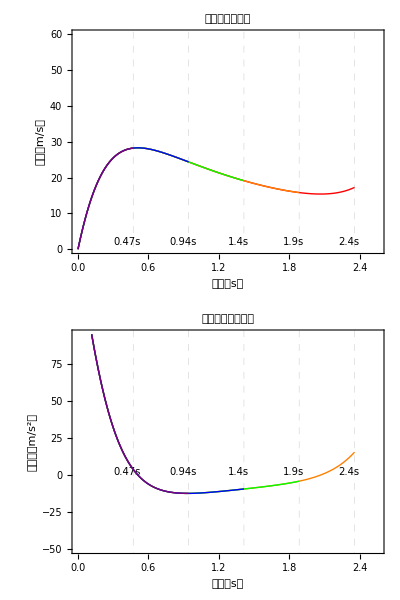

```mathematica
conVVar=Block[{P0=101325,M0=50,ρ0=1.2,μ=0.6,A=0.001,A0=1,C0=2,pi=10000000,M=2.9*10^-2,R=8.31,T=303},
Grid[{{pltStyle={Red,Orange,Green,Blue,Purple};
conVVarGridLinesX={};
Show[Table[
m0= pi/(1/M(R T)/V);
conVVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conVVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
conVVarGridLinesX=Append[conVVarGridLinesX,{conVVartempt2,Dashed}];
Plot[v[t]/.conVVarVSol
,{t,0,conVVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]},PlotRange->{{0,conVVartempt2+0.2},{0,60}},PlotStyle->pltStyle[[Position[{0.1,0.08,0.06,0.04,0.02},V][[1]][[1]]      ]],Frame->True,FrameLabel->{"时间（s）","速度（m/s）"},
ImageSize->imgSize,PlotLabel->"速度随时间变化",ImagePadding->{{40,10},{40,10}}]
,{V,{0.1,0.08,0.06,0.04,0.02}}],
Prolog->Table[Inset[Style[ToString[NumberForm[conVVarVelTableTemp,2]]<>"s",10],{conVVarVelTableTemp-0.05,2},{Center,Center}],{conVVarVelTableTemp,Select[Flatten[conVVarGridLinesX],NumberQ]}],
GridLines->{conVVarGridLinesX,{}}
]
},{
Show[
Table[
Clear[conVVartempt2];
conVVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conVVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
m0= pi/(1/M(R T)/V);
Plot[Evaluate[accelerationtemp2=D[v[t]/.conVVarVSol[[1]],t]],{t,0,conVVartempt2},PlotStyle->pltStyle[[Position[{0.1,0.08,0.06,0.04,0.02},V][[1]][[1]]      ]],PlotRange->{{0,Max[Select[Flatten[conVVarGridLinesX],NumberQ]]+0.2},{-50,95}},
Frame->True,FrameLabel->{"时间（s）","加速度（m/s^2）"},GridLines->{{{conVVartempt2,Dashed}},{{accelerationtemp2/.{t->conVVartempt2},Dashed}}},Prolog->Table[Inset[Style[ToString[NumberForm[conVVarAcceTableTemp,2]]<>"s",10],{conVVarAcceTableTemp-0.05,2},{Center,Center}],{conVVarAcceTableTemp,Select[Flatten[conVVarGridLinesX],NumberQ]}],ImageSize->imgSize,PlotLabel->"加速度随时间变化",ImagePadding->{{40,10},{40,10}}],{V,{0.1,0.08,0.06,0.04,0.02}}],
GridLines->{conVVarGridLinesX,{}}]
}}]
]
```

气瓶内的压强

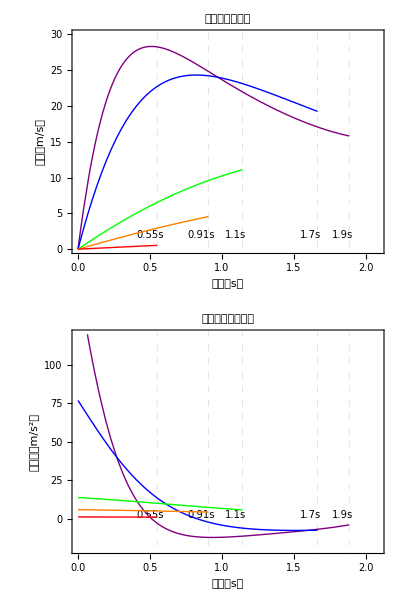

```mathematica
conpiVar=Block[{P0=101325,M0=50,ρ0=1.2,μ=0.6,A=0.001,A0=1,C0=2,M=2.9*10^-2,R=8.31,T=303,V=0.08},
Grid[{{pltStyle={Red,Orange,Green,Blue,Purple};
conpiVarGridLinesX={};
Show[Table[
m0= pi/(1/M(R T)/V);
conpiVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conpiVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
conpiVarGridLinesX=Append[conpiVarGridLinesX,{conpiVartempt2,Dashed}];
Plot[v[t]/.conpiVarVSol
,{t,0,conpiVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]},PlotRange->{{0,conpiVartempt2+0.2},{0,30}},PlotStyle->pltStyle[[Position[{200000,500000,1000000,5000000,10000000},pi][[1]][[1]]      ]],Frame->True,FrameLabel->{"时间（s）","速度（m/s）"},
ImageSize->imgSize,PlotLabel->"速度随时间变化",ImagePadding->{{40,10},{40,10}}]
,{pi,{10000000,5000000,1000000,500000,200000}}],
Prolog->Table[Inset[Style[ToString[NumberForm[conpiVarVelTableTemp,2]]<>"s",10],{conpiVarVelTableTemp-0.05,2},{Center,Center}],{conpiVarVelTableTemp,Select[Flatten[conpiVarGridLinesX],NumberQ]}],
GridLines->{conpiVarGridLinesX,{}}
]
},{
Clear[m0,conpiVartempt2];
Show[
Table[
m0= pi/(1/M(R T)/V);
conpiVarVSol=NDSolve[{airDragPDropVEqn,v[0]==0},v,{t,0,conpiVartempt2=t/.FindRoot[MinValue[airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],t]==airDragPDropMassFunc[pi,m0,A,μ,ρ0,P0],{t,1}]}];
Plot[Evaluate[conpiVaraccelerationtemp2=D[v[t]/.conpiVarVSol[[1]],t]],{t,0,conpiVartempt2},PlotStyle->pltStyle[[Position[{200000,500000,1000000,5000000,10000000},pi][[1]][[1]]      ]],
PlotRange->{{0,conpiVartempt2+0.2},{-20,120}},
Frame->True,FrameLabel->{"时间（s）","加速度（m/s^2）"},GridLines->{{{conpiVartempt2,Dashed}},{{conpiVaraccelerationtemp2/.{t->conpiVartempt2},Dashed}}},ImageSize->imgSize,PlotLabel->"加速度随时间变化",ImagePadding->{{40,10},{40,10}}],
{pi,{10000000,5000000,1000000,500000,200000}}],
Prolog->Table[Inset[Style[ToString[NumberForm[conpiVarAcceTableTemp,2]]<>"s",10],{conpiVarAcceTableTemp-0.05,2},{Center,Center}],{conpiVarAcceTableTemp,Select[Flatten[conpiVarGridLinesX],NumberQ]}],
GridLines->{conpiVarGridLinesX,{}}]
}}]
]
```

## 正文主要内容所需图表

正文大致分为两部分

立体行动装置的使用策略

立体行动装置的缺憾

### 对于第一部分，分析以下几点

使用者的体重以及其他的所有的装备的重量（包括气瓶）

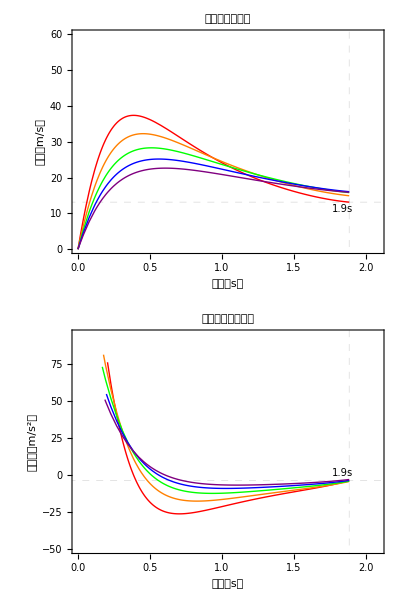

```mathematica
conM0Var
```

气瓶的大小

```mathematica
conVVar
```

-Graphics-

气瓶内的压强

```mathematica
conpiVar
```

-Graphics-

喷气孔的面积

```mathematica
conAVar
```

-Graphics-

### 优势是

初始的机动性好，加速度大，可以很快的改变运动状态

### 对于缺憾，分析以下几点

气体很快就喷完了！

```mathematica
conGasCons
```

-Graphics-

### 有没有可能真的让这个能用呢？

可以使用减压阀
像动画片里面那样断断续续的喷
可以使用其他密度的气体

## Examples

We take an example here.

Mass of equipment with everything attached including the gas: 10kg

## Draft

```mathematica
Manipulate[Block[{P0=101325},Plot[(2 A (P-P0) μ^2)/(M0+m0-(√2 A P t μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0),{t,0,(M0+m0)/((√2 A P μ √(((P-P0) P0)/(P ρ0)) ρ0)/P0)},Frame->True,FrameLabel->{"Time","Acceleration"},ImageSize->imgSize*0.8]],{{μ,0.6,"Leakage Constant"},0.6,0.62,0.01},{{P,200000,"Constant Pressure"},101325,1000000,1000},{{m0,10,"Initial Mass of Equipment"},1,60,1},{{ρ0,1.16,"Density of Air"},1.42,1.14,-0.01},{{A,0.01,"Area of Outlet"},0.001,1},{{M0,50,"Mass of Everything Else"},10,100,1}]
```

### Draft for velocity calculation: Consider air drag, pressure drop when using gas

```mathematica
airDragPDropVSol=NDSolve[{
(0.0001976646847218969 √(1-(3.7344008769107955*^6 ⅇ^(3.169233459805099 t))/(3.6668713384455955*^8+1.8672004384553977*^6 ⅇ^(3.169233459805099 t)+2376.9837796092033 ⅇ^(6.338466919610198 t))) √(ⅇ^(-3.169233459805099 t) (3.6668713384455955*^8+1.8672004384553977*^6 ⅇ^(3.169233459805099 t)+2376.9837796092033 ⅇ^(6.338466919610198 t)) (-101325+0.027132866379310346 ⅇ^(-3.169233459805099 t) (3.6668713384455955*^8+1.8672004384553977*^6 ⅇ^(3.169233459805099 t)+2376.9837796092033 ⅇ^(6.338466919610198 t))))-1.2 v[t]^2)/(50+(ⅇ^(-3.169233459805099 t) (3.6668713384455955*^8+1.8672004384553977*^6 ⅇ^(3.169233459805099 t)+2376.9837796092033 ⅇ^(6.338466919610198 t)))/40000000)==v'[t],
v[0]==0
}
,v,{t,0,0.1}]
```

{{v→InterpolatingFunction[{{0.,0.1}},<>]}}

```mathematica
v[t]/.airDragPDropVSol
```

{InterpolatingFunction[{{0.,0.1}},<>][t]}

```mathematica
accetemp=
D[v[t]/.airDragPDropVSol[[1]],t]
accetemp/.{t->0.05}
```

InterpolatingFunction[{{0.,0.1}},<>][t]

173.213

```mathematica
D[veltemp'[t],t]
```

InterpolatingFunction[{{0.,0.1}},<>][t]''[t]+(InterpolatingFunction[{{0.,0.1}},<>][t]'' InterpolatingFunction[{{0.,0.1}},<>][t])[t]

```mathematica
v[0.1]/.airDragPDropVSol
```

{17.3225}

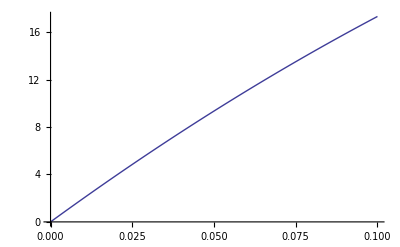

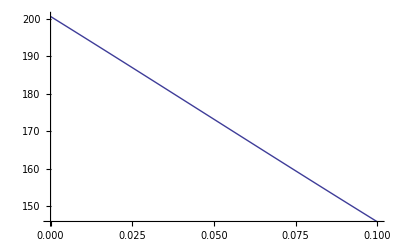

```mathematica
Plot[v[t]/.airDragPDropVSol,{t,0,0.1}]
Plot[Evaluate[D[v[t]/.airDragPDropVSol[[1]],t]],{t,0,0.1}]
```

```mathematica
tabletemp=Table[v[t]/.airDragPDropVSol[[1]],{t,0,0.1,0.0001}];
tabletemplength=Length[%]
```

1001

```mathematica
(tabletemp[[11]]-tabletemp[[10]])/0.0001
(tabletemp[[tabletemplength]]-tabletemp[[tabletemplength-1]])/0.0001
```

200.088

145.918